# Index of Conicidence

## References

http://www.murky.org/blg/2004/10/index-of-coincidences-a-worked-example/

http://en.wikipedia.org/wiki/Index_of_coincidence

http://practicalcryptography.com/cryptanalysis/text-characterisation/index-coincidence/

## kappaIC

```mathematica
testText = DeleteCases[Characters["QPWKA LVRXC QZIKG RBPFA EOMFL  JMSDZ VDHXC XJYEB IMTRQ WNMEA
IZRVK CVKVL XNEIC FZPZC ZZHKM  LVZVZ IZRRQ WDKEC HOSNY XXLSP
MYKVQ XJTDC IOMEE XDQVS RXLRL  KZHOV"]," "]
```

{Q,P,W,K,A,L,V,R,X,C,Q,Z,I,K,G,R,B,P,F,A,E,O,M,F,L,J,M,S,D,Z,V,D,H,X,C,X,J,Y,E,B,I,M,T,R,Q,W,N,M,E,A,
,I,Z,R,V,K,C,V,K,V,L,X,N,E,I,C,F,Z,P,Z,C,Z,Z,H,K,M,L,V,Z,V,Z,I,Z,R,R,Q,W,D,K,E,C,H,O,S,N,Y,X,X,L,S,P,
,M,Y,K,V,Q,X,J,T,D,C,I,O,M,E,E,X,D,Q,V,S,R,X,L,R,L,K,Z,H,O,V}

```mathematica
testTextShifted=RotateRight[testText,1]
```

{V,Q,P,W,K,A,L,V,R,X,C,Q,Z,I,K,G,R,B,P,F,A,E,O,M,F,L,J,M,S,D,Z,V,D,H,X,C,X,J,Y,E,B,I,M,T,R,Q,W,N,M,E,A,
,I,Z,R,V,K,C,V,K,V,L,X,N,E,I,C,F,Z,P,Z,C,Z,Z,H,K,M,L,V,Z,V,Z,I,Z,R,R,Q,W,D,K,E,C,H,O,S,N,Y,X,X,L,S,P,
,M,Y,K,V,Q,X,J,T,D,C,I,O,M,E,E,X,D,Q,V,S,R,X,L,R,L,K,Z,H,O}

```mathematica
kappaIC[text_,shift_,c_:26]:= Module[{textL=Select[Characters[ToUpperCase[text]],LetterQ]},Divide[Sum[If[textL[[i]]==textL[[Mod[i+shift,Length[textL]]]], 1, 0],{i,1,Length[textL]}],(Length[textL]/c)]]
```

```mathematica
testText = "QPWKA LVRXC QZIKG RBPFA EOMFL  JMSDZ VDHXC XJYEB IMTRQ WNMEA
IZRVK CVKVL XNEIC FZPZC ZZHKM  LVZVZ IZRRQ WDKEC HOSNY XXLSP
MYKVQ XJTDC IOMEE XDQVS RXLRL  KZHOV";
```

```mathematica
kappaIC[testText,1]
```

4+If[O==List,1,0]

```mathematica
RotateRight[{a,b,c,d,e},2][[2]]
```

e

```mathematica
kappaIC[text_,shift_,c_:26]:= Module[{textL=Select[Characters[ToUpperCase[text]],LetterQ]},Divide[Sum[If[textL[[i]]==RotateRight[textL,shift][[i]], 1, 0],{i,1,Length[textL]}],(Length[textL]/c)]]
```

```mathematica
kappaIC[testText,1]
```

4+If[O==List,1,0]

```mathematica
Clear[kappaIC]
```

```mathematica
kappaIC[text_,shift_,c_:26]:= Module[{textL=Select[Characters[ToUpperCase[text]],LetterQ]},Divide[Sum[If[textL[[i]]==RotateRight[textL,shift][[i]], 1, 0],{i,1,Length[textL]}],(Length[textL]/c)]] //N
```

```mathematica
kappaIC[testText,1]
```

0.8

```mathematica
kappaICTable[text_,maxShifts_,c_:26]:=ParallelTable[{shift, kappaIC[text,shift,c]},{shift,1,maxShifts}] //TableForm
```

```mathematica
kappaICTable[testText, 15]
```

1 | 0.8
2 | 1.6
3 | 1.
4 | 0.6
5 | 0.8
6 | 0.8
7 | 0.6
8 | 0.8
9 | 1.
10 | 1.4
11 | 1.2
12 | 0.2
13 | 1.2
14 | 0.8
15 | 1.6

```mathematica
kappaICPlot[text_,maxShifts_,c_:26]:=Plot[kappaIC[text,shift,c],{shift,1,maxShifts}]
```

```mathematica
kappaICPlot[testText,15]
```

RotateRight::rspec: Rotation specification {1.00029} should be a machine-sized integer or list of machine-sized integers.

General::stop: Further output of RotateRight :: rspec will be suppressed during this calculation.

Part::partw: Part 3 of RotateRight[{"Q", "P", "W", "K", "A", "L", "V", "R", "X", "C", "Q", "Z", "I", "K", "G", "R", "B", "P", "F", "A", "E", "O", "M", "F", "L", "J", "M", "S", "D", "Z", "V", "D", "H", "X", "C", "X", "J", "Y", "E", "B", "I", "M", "T", "R", "Q", "W", "N", "M", "E", "A", « 80 »}, 1.00029] does not exist.

Part::partw: Part 4 of RotateRight[{"Q", "P", "W", "K", "A", "L", "V", "R", "X", "C", "Q", "Z", "I", "K", "G", "R", "B", "P", "F", "A", "E", "O", "M", "F", "L", "J", "M", "S", "D", "Z", "V", "D", "H", "X", "C", "X", "J", "Y", "E", "B", "I", "M", "T", "R", "Q", "W", "N", "M", "E", "A", « 80 »}, 1.00029] does not exist.

Part::partw: Part 5 of RotateRight[{"Q", "P", "W", "K", "A", "L", "V", "R", "X", "C", "Q", "Z", "I", "K", "G", "R", "B", "P", "F", "A", "E", "O", "M", "F", "L", "J", "M", "S", "D", "Z", "V", "D", "H", "X", "C", "X", "J", "Y", "E", "B", "I", "M", "T", "R", "Q", "W", "N", "M", "E", "A", « 80 »}, 1.00029] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

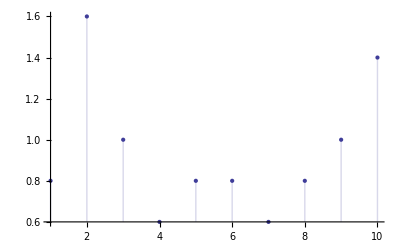

```mathematica
DiscretePlot[kappaIC[testText,i],{i,1,10}]
```

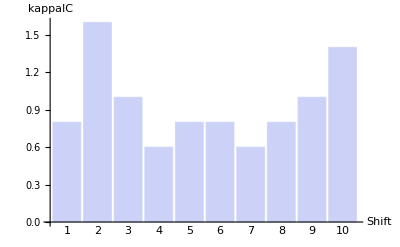

```mathematica
BarChart[ParallelTable[kappaIC[testText,i],{i,1,10}],{ChartLabels->Placed[Range[1,10],Below],AxesLabel->{"Shift","kappaIC"}}]
```

```mathematica
kappaICPlot[text_,maxShifts_,c_:26]:=BarChart[ParallelTable[kappaIC[text,shift,c],{shift,1,maxShifts}],{ChartLabels->Placed[Range[1,maxShifts],Below],AxesLabel->{"Shift","kappaIC"}}]
```

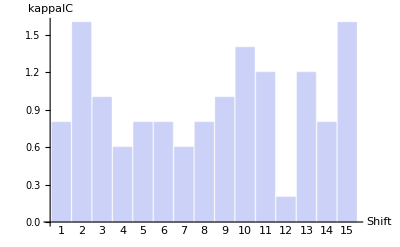

```mathematica
kappaICPlot[testText,15]
```

## deltaIC

```mathematica
testText = "QPWKA LVRXC QZIKG RBPFA EOMFL  JMSDZ VDHXC XJYEB IMTRQ WNMEA
IZRVK CVKVL XNEIC FZPZC ZZHKM  LVZVZ IZRRQ WDKEC HOSNY XXLSP
MYKVQ XJTDC IOMEE XDQVS RXLRL  KZHOV";
```

```mathematica
deltaIC[text_,c_:26]:=Divide[Sum[n(n-1),{n,1,c}],((N*(N-1))/c)]
```

```mathematica
numToLetter[num_,letters_:CharacterRange["a","z"]]:=letters[[num]]
```

```mathematica
numToLetter[2]
```

b

```mathematica
deltaIC[text_,c_:26,letters_:CharacterRange["a","z"]]:=Module[{textL=Select[Characters[ToLowerCase[text]],LetterQ]},Divide[Sum[Count[textL,numToLetter[l,letters]]*(Count[textL,numToLetter[l,letters]]-1),{l,1,c}],((Length[textL]*(Length[textL]-1))/c)]] //N
```

```mathematica
deltaIC[testText]
```

1.11628

Verify against Practical Cryptography Javascript IC Calculator (doen’t normalize with c)

```mathematica
Module[{textL=Select[Characters[ToLowerCase["Defend the east wall of the castle"]],LetterQ]},Divide[Sum[Count[textL,numToLetter[l]]*(Count[textL,numToLetter[l]]-1),{l,1,26}],Length[textL]*(Length[textL]-1)]] //N
```

0.0820106

## deltaBarIC

```mathematica
testText="QPWKA LVRXC QZIKG RBPFA EOMFL  JMSDZ VDHXC XJYEB IMTRQ WNMEA
IZRVK CVKVL XNEIC FZPZC ZZHKM  LVZVZ IZRRQ WDKEC HOSNY XXLSP
MYKVQ XJTDC IOMEE XDQVS RXLRL  KZHOV";
```

```mathematica
deltaBarIC[text_,keyLength_,c_:26,letters_:CharacterRange["a","z"]]:= Mean[Table[deltaIC[subText,c,letters],{k,1,keyLength}]]
```

```mathematica
Partition[Select[Characters[ToLowerCase[testText]],LetterQ],5] //MatrixForm
```

(q | p | w | k | a
l | v | r | x | c
q | z | i | k | g
r | b | p | f | a
e | o | m | f | l
j | m | s | d | z
v | d | h | x | c
x | j | y | e | b
i | m | t | r | q
w | n | m | e | a
i | z | r | v | k
c | v | k | v | l
x | n | e | i | c
f | z | p | z | c
z | z | h | k | m
l | v | z | v | z
i | z | r | r | q
w | d | k | e | c
h | o | s | n | y
x | x | l | s | p
m | y | k | v | q
x | j | t | d | c
i | o | m | e | e
x | d | q | v | s
r | x | l | r | l
k | z | h | o | v)

```mathematica
Out[23][[All,2]]
```

{p,v,z,b,o,m,d,j,m,n,z,v,n,z,z,v,z,d,o,x,y,j,o,d,x,z}

```mathematica
deltaBarIC[text_,keyLength_,c_:26,letters_:CharacterRange["a","z"]]:= Module[{textM=Partition[Select[Characters[ToLowerCase[text]],LetterQ],keyLength]},Mean[Table[deltaIC[StringJoin[textM[[All,k]]],c,letters],{k,1,keyLength}]]]
```

```mathematica
deltaBarIC[testText,1]
```

1.11628

```mathematica
deltaBarICTable[text_,maxKeyLength_,c_:26,letters_:CharacterRange["a","z"]]:=ParallelTable[{keyLength,deltaBarIC[text,keyLength,c,letters]},{keyLength,1,maxKeyLength}] //TableForm
```

```mathematica
deltaBarICTable[testText,10]
```

1 | 1.11628
2 | 1.1875
3 | 1.03654
4 | 1.19254
5 | 1.824
6 | 1.03175
7 | 1.01961
8 | 1.08333
9 | 1.1746
10 | 2.06667

```mathematica
deltaBarICPlot[text_,maxKeyLength_,c_:26,letters_:CharacterRange["a","z"]]:=BarChart[ParallelTable[deltaBarIC[text,keyLength,c,letters],{keyLength, 1,maxKeyLength}],{ChartLabels->Placed[Range[1,maxKeyLength],Below],AxesLabel->{"Key Length","deltaBarIC"}}]
```

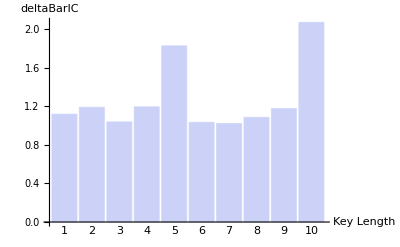

```mathematica
deltaBarICPlot[testText,10]
```